## MKP pre 1D rovnicu vedenia tepla

### Integrácia cez kvadratúry, aproximácia integrálu, súčet vážených hodnôt funkcie

```mathematica
GaussNodesWeights[n_]:=Module[{x,P,dP,xi,wi},
P=LegendreP[n,x]; (*Legendreho polynóm n-teho stupňa*)
dP=D[P,x];
xi=x/. NSolve[P==0&&-1<x<1,x]; (*nájde všetky korene Pn na (-1,1), gaussove uzly*)
xi=N[xi];
wi=N[2/((1-xi^2) (dP/. x->xi)^2)]; (*váhy*)
Transpose[{xi,wi}] (*zoznam párov xi-uzly, wi-váhy*)
];

{xi,wi}=Transpose[GaussNodesWeights[3]]; (*3 bodová*)

(*Numerická Gaussova kvadratúra na interval[a,b]*)
GaussQuad[f_,x_,a_,b_]:=
Module[{c=(a+b)/2, (*stred intervalu*)
h=(b-a)/2}, (*1/2 intervalu*)
N@(h*Total[wi*(f/. x->(c+h*xi))]) (*za x dosadím všetky body c + hxi​, ich suma*)
];
```

Parametre ulohy

```mathematica
(*−d/dx(a(x)du/dx(x))=f(x)*)
xL=0;xP=1;(*Hranice vypoctovej oblasti*)
a[x_]=(1+x);(*materialova charakteristika*)
f[x_]=-18x^2;(*prava strana*)
α1=1;β1=0;g1=1;(*Paramtre ľavej OP, (n=-1), mením znamienko*)
α2=0;β2=1;g2=0;(*Paramtre pravej OP, (n=+1)*)
```

Presne riesenie

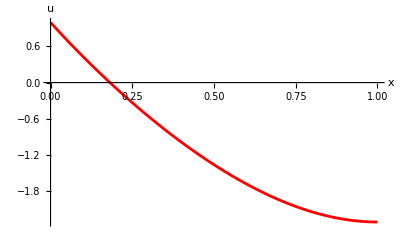

```mathematica
Rovnica=-D[a[x]u'[x],x]==f[x];
riesenie=DSolve[{
Rovnica,
α1 u[xL]+β1 (-a[xL]u'[xL])==g1,
α2 u[xP]+β2 (a[xP]u'[xP])==g2
},u[x],x];
uA[x_]=u[x]/.riesenie[[1]];
plotA=Plot[uA[x], {x,xL,xP},AxesLabel->{Style[x,Large],Style[u,Large]},PlotStyle->Red]
```

MKP, diskretizacia oblasti

```mathematica
s=1;(*stupeň elementu:1=lineárny (2 prvky na elemente),2=kvadratický...*)
NN=4;(*počet elementov, počet rovníc*)
n=s*NN+1;(*počet globálnych uzlov, pre lin = NN +1*)
H=(xP-xL)/NN;(*dĺžka jedného elementu*)
h = H/s;(*vzdialenosť susedných globálnych uzlov*)
```

MKP, zostrojenie aproximacnych funkcii (Lagrangeov tvar)

{{-4 (-1/4+x),4 x},{-4 (-1/2+x),4 (-1/4+x)},{-4 (-3/4+x),4 (-1/2+x)},{-4 (-1+x),4 (-3/4+x)}}

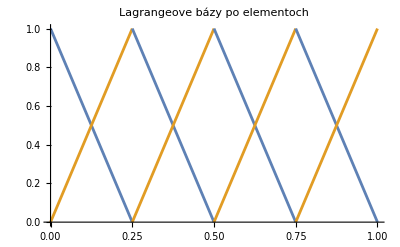

```mathematica
(*VŠETKY globálne uzly*)
uzly=Table[xL+j*h,{j,0,NN*s}];   (*dĺžka=NN*s+1*)

(*pre každý element zoberie (s + 1) po sebe idúcich uzlov*)
uzlyNaElemente[e_]:=uzly[[(e-1)*s+1;;(e-1)*s+s+1]];(*zoznam dĺžky s+1*)

(*globálne indexy uzlov elementu e*)
(*vracia globálne uzly, ktoré danému elementu patria*)
(*globIdx[2]={3,4,5} -> (U1, U2, U3 na tomto e)*)
globIdx[e_]:=Range[(e-1)*s+1,(e-1)*s+s+1];


(*aproximačné funkcie*)
(*loc - zoznam uzlov na elemente*)
psiLagrange[x_,loc_,i_]:=
Product[
If[j==i,1, (*kronekerova delta*)
(x-loc[[j]])/(loc[[i]]-loc[[j]])],
{j,1,Length[loc]}
]; (*vráti symbolickú apr.f.*)

(*všetky aproximačné funkcie na všetkých elementoch*)
(*dvojitý zoznam e - element=1,...,NN, i - lokálna báza na elemente*)
(*{element 1-jeho lok.báza}, {element 2-jeho lok.báza}*)
psiVsetky=
Table[
With[
{loc=uzlyNaElemente[e]},
Table[
psiLagrange[x,loc,i],{i,1,Length[loc]
}
]
],
{e,1,NN}
]

(*derivácie aproximačných funkcií*)
dpsiVsetky=D[psiVsetky,x];


Show[Table[With[{loc=uzlyNaElemente[e],funs=psiVsetky[[e]]},Plot[Evaluate[funs],{x,First[loc],Last[loc]},PlotLegends->None]],{e,1,NN}],PlotRange->All,PlotLabel->"Lagrangeove bázy po elementoch"]
```

MKP, zostrojenie lokalnych matic a pravych stran

```mathematica
(*zintegrujem cez celý element*)
(*pre každý element integrujem dvojicu {Ke,fe}*)
elementMatrices=
Table[
Module[{loc,m,xA,xB,psi,dpsi,Ke,fe},
loc=uzlyNaElemente[e]; (*lokálne uzly na elemente e*)
m=Length[loc]; (*počet uzlových bodov -apr.f. na elemente*)
xA=First[loc];(*začiatok, koniec elementu*)
xB=Last[loc]; 
psi=psiVsetky[[e]]; (*zoznam pre element e*)
dpsi=dpsiVsetky[[e]];

(*Lokálna tuhosť Ke*)
Ke=N@Table[GaussQuad[a[x]*dpsi[[i]]*dpsi[[j]],x,xA,xB],
{i,m},{j,m}
];
(*lokálny vektor fe*)
fe=N@Table[GaussQuad[f[x]*psi[[i]],x,xA,xB],{i,m}];

{Ke,fe}],{e,1,NN}(*zoznam {K1, f1}, {K2, f2}*)
];

(*prvý index element, druhý index či K alebo f*)
elementMatrices[[1,1]]//MatrixForm   (*K1–tuhosť 1. elementu*)
elementMatrices[[1,2]]                 (*f1–pravá strana 1. elementu*)
elementMatrices[[2,1]]//MatrixForm   (*K2*)
elementMatrices[[2,2]]   (*f2*)
```

(4.5 | -4.5
-4.5 | 4.5)

{-0.0234375,-0.0703125}

(5.5 | -5.5
-5.5 | 5.5)

{-0.257812,-0.398437}

MKP, zostrojenie globalnych matic a pravych stran

```mathematica
(*SPOJENIE----------------------------------------------------
- prenesiem lokálne príspevky do globálnych indexov
*)
Clear[K,F,GlobK,GlobF,U];

GlobK=ConstantArray[0.,{n,n}]; (*n-počet globálnych uzlov*)
GlobF=ConstantArray[0.,n];

(* hladám spoločné globálne uzly*)
Do[
Module[{Ke,fe,g},
{Ke,fe}=elementMatrices[[e]];(* lokálne príspevky elementu e*)
g=globIdx[e]; (*globálne index daného elementu e*)
(*Prenesiem Ke Ff DO GLOBÁLU*)
Do[
GlobK[[g[[i]],g[[j]]]]+=Ke[[i,j]],{i,Length[g]},
{j,Length[g]}];
Do[
GlobF[[g[[i]]]]              +=fe[[i]],
{i,Length[g]}];
],(*zdielané uzly = súčet prvkov viacerých elementov*)
{e,1,NN}
];

(*K11^2 + K22^1 = K22^glob*)
(*f1^2 + f2^1 = f2^glob*)
GlobK //MatrixForm
GlobF//MatrixForm

(*uloženie „originálu“ pred OP–na reakcie, zložené len z elementov*)
K0=GlobK;F0=GlobF;
```

(4.5 | -4.5 | 0. | 0. | 0.
-4.5 | 10. | -5.5 | 0. | 0.
0. | -5.5 | 12. | -6.5 | 0.
0. | 0. | -6.5 | 14. | -7.5
0. | 0. | 0. | -7.5 | 7.5)

(-0.0234375
-0.328125
-1.17187
-2.57812
-1.89844)

MKP, zahrnutie okrajovych podmienok

```mathematica
(*OP----------------------------------------------------
- dirichlet prepisuje
- Neumann pripočíta
*)
(*ĽAVÝ OKRAJ–Dirichlet u(0)=g1/α1=0, na prvo uzle, predpisujem U[1] = val*)
If[α1!=0,
val=g1/α1;
GlobF=GlobF-GlobK[[All,1]]*val;
GlobK[[1,All]]=0; 
GlobK[[All,1]]=0; 
GlobK[[1,1]]=1; (*koeficient pri 1. U1 = val*)
GlobF[[1]]=val;
];

(*ĽAVÝ OKRAJ–NEUMANN - MÍNUS, vonkajšia normála n = -1*)
If[β1!=0,
GlobK[[1,1]]+=α1/β1;
GlobF[[1]]-=g1/β1;];


(*PRAVÝ OKRAJ Dirichlet u(L)=g2/α2, na poslednom uzle n*)
If[α2!=0,
val=g2/α2;
(*zoberiem časť, kde je Ki,n.Un, za Un dosadim val, prenesiem na pravú stranu*)
(*inak by som prišla o príspevok pri následnom nulovaní*)
GlobF=GlobF-GlobK[[All,n]]*val;
GlobK[[n,All]]=0;
GlobK[[All,n]]=0;
GlobK[[n,n]]=1;
GlobF[[n]]=val;
];

(*PRAVÝ OKRAJ NEUMANN, PLUS*)
If[β2!=0,
GlobK[[n,n]]+=α2/β2;
GlobF[[n]]+=g2/β2;
];
```

```mathematica
MatrixForm[GlobK];
GlobF//MatrixForm;
```

MKP, riesenie rovnic, konstrukcia priblizneho riesenia, zobrazenie presneho aj priblizneho riesenia

{1.,-0.328125,-1.35511,-2.04382,-2.29694}

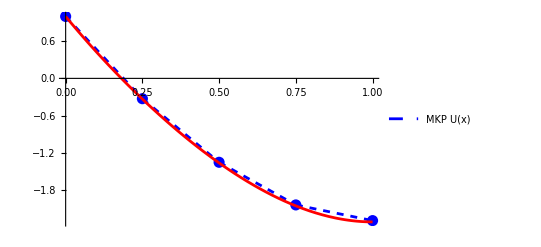

```mathematica
(* výpočet vektora uzlových hodnôt U1,U1,...,aproximácie rešenie v glob.uzl.bodoch*)
U=LinearSolve[N@GlobK,N@GlobF] 

Clear[uMKP]
(*rekonštrukcia*)
uMKP[x_]:=Piecewise@Table[
With[
{loc=uzlyNaElemente[e],(*uzly elementu*)
idx=globIdx[e]}                  (*globálne indexy tých uzlov*),
{
(*zosumujem skalárny súčin U.psi*)
U[[idx]].psiVsetky[[e]],(*psiVsetky -> vektor aproximacnych funkcii*)
loc[[1]]<=x<=loc[[-1]]  (*interval elementu–všade uzavretý*)
}
],{e,1,NN}
];
plotU=Plot[uMKP[x],{x,xL,xP},PlotStyle->{Blue,Dashed},PlotLegends->{"MKP U(x)"},PlotRange->All]; (*súvislá MKP aproximácia*)

plotPts=ListPlot[Transpose[{uzly,U}],PlotStyle->{Blue,PointSize[0.02]}];(*uzlvé hodnoty, hodnoty v uzloch, vypočítané, uzly rozdelené*)

Show[plotU,plotPts, plotA]
```

MKP, vypocet chyb a EOC (m=1,2,4,8,16,32)

Vo vseobecnosti ma MKP v L2-chybe presnost radu
	p = (stupen elementov) + 1 (cize s+1)

a v Energetickej chybe radu
	p = (stupen elementov) - (rad rovnice)/2 + 1 (cize s u nas)

-Graphics-

```mathematica
(*pred výpočtami si pripravím prázdne polia na chyby*)
L2pole={};
ENpole={};
```

### Chyby

```mathematica
(*L2 chyba aproximácia - analytické riešenie*)
(*„Priemerná“chyba v hodnote funkcie*)
L2=Sqrt@NIntegrate[(uMKP[x]-uA[x])^2,{x,xL,xP}]
uMKPder[x_]:=D[uMKP[x],x];
duA[x_]:= D[uA[x],x];

energetickaChyba=Sqrt@NIntegrate[a[x] (uMKPder[x]-duA[x])^2,{x,xL,xP}]

L2pole=Append[L2pole,L2];
ENpole=Append[ENpole,energetickaChyba];

EOCL2=Log[L2pole[[1]]/L2pole[[2]]]/Log[2]
EOCEN=Log[ENpole[[1]]/ENpole[[2]]]/Log[2]
```

0.0455456

0.557792

1.97438

0.971449

### Q - čka

-Graphics-

```mathematica
(*Dopočítanie Q-čok, sekundárne neznáme, q(x)=a(x)du/dx(x)*)
Odpočet=K0.U-F0;   (*čistá tuhosť, pred OP, čistá PS*)
Q11=Odpočet[[1]]  (*Q naľavo*)
Q2N = Odpočet[[-1]] (*Q napravo*)
```

6.

-8.88178×10^-16